{{y[x]→InterpolatingFunction[…][x]}}

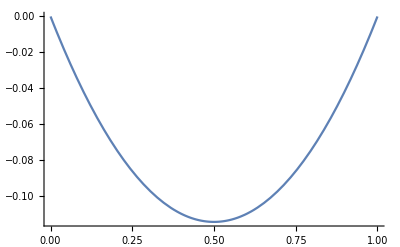

```mathematica
Clear["Global`*"]
s=NDSolve[{y''[x]==y[x]^2+y[x]+1,y[0]==0,y[1]==0},y[x],{x,0,1}]
Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```